```mathematica
rapp[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]/x2[[i,2]]},{i,1,Length[x1]}]
absrapp[x1_,x2_]:=Table[{x1[[i,1]],Abs[x1[[i,2]]/x2[[i,2]]]},{i,1,Length[x1]}]
mult[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]*x2[[i,2]]},{i,1,Length[x1]}]
sum[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]+x2[[i,2]]},{i,1,Length[x1]}]
sumlist[x1_]:=Table[{x1[[1,i,1]],x1[[1,i,2]]+x1[[2,i,2]]+x1[[3,i,2]]},{i,1,Length[x1[[1]]]}]
coeff[x1_,c_]:=Table[{x1[[i,1]],x1[[i,2]]*c},{i,1,Length[x1]}]
sumconst[x1_,c_]:=Table[{x1[[i,1]],x1[[i,2]]+c},{i,1,Length[x1]}]
diff[x1_,x2_]:=Table[{x1[[i,1]],x1[[i,2]]-x2[[i,2]]},{i,1,Length[x1]}]
joinbin[x_,n_]:=Map[{(Plus@@#)[[1]]/n,(Plus@@#)[[2]]}&,Partition[x,n]]
```

```mathematica
(* CONYsbaglatamumuraw=Import["/Users/pagani/mu-vbf/Confronti con Marco/fromcluster/firstrun/mumu.dat"];
muaraw=Import["/Users/pagani/mu-vbf/Confronti con Marco/fromcluster/firstrun/mua_v2.dat"];
aaraw=Import["/Users/pagani/mu-vbf/Confronti con Marco/fromcluster/firstrun/aa.dat"];


mumuraw=Import["/Users/pagani/mu-vbf/Confronti con Marco/fromcluster/1TeV/mumufortt/oneTeV.dat"];
muaraw=Import["/Users/pagani/mu-vbf/Confronti con Marco/fromcluster/1TeV/muafortt/oneTeV_corrected.dat"];
aaraw=Import["/Users/pagani/mu-vbf/Confronti con Marco/fromcluster/1TeV/aafortt/oneTeV.dat"]
*)

mumuraw=Import["/Users/pagani/mu-vbf/Confronti con Marco/fromcluster/Ycorrected10TeV/mumufortt/Ycorrect500Kat10TeV.dat"];
muaraw=Import["/Users/pagani/mu-vbf/Confronti con Marco/fromcluster/Ycorrected10TeV/muafortt/Ycorrect500Kat10TeV.dat"];
aaraw=Import["/Users/pagani/mu-vbf/Confronti con Marco/fromcluster/Ycorrected10TeV/aafortt/Ycorrect500Kat10TeV.dat"];
```

```mathematica
mumuraw=Import["/Users/pagani/mu-vbf/Confronti con Marco/fromcluster/Ycorrected1TeV/mumufortt/oneTeVyok.dat"];
muaraw=Import["/Users/pagani/mu-vbf/Confronti con Marco/fromcluster/Ycorrected1TeV/muafortt/oneTeVyok.dat"];
aaraw=Import["/Users/pagani/mu-vbf/Confronti con Marco/fromcluster/Ycorrected1TeV/aafortt/oneTeVyok.dat"];
```

```mathematica
mumu=Table[{0.1*2^(i-6),mumuraw[[i,3]]},{i,1,Length[muaraw]}];
mumuerror=Table[{0.1*2^(i-6),mumuraw[[i,4]]},{i,1,Length[muaraw]}];
mua=Table[{0.1*2^(i-6),muaraw[[i,3]]},{i,1,Length[muaraw]}];
muaerror=Table[{0.1*2^(i-6),muaraw[[i,4]]},{i,1,Length[muaraw]}];
aa=Table[{0.1*2^(i-6),aaraw[[i,3]]},{i,1,Length[muaraw]}];
aaerror=Table[{0.1*2^(i-6),aaraw[[i,4]]},{i,1,Length[muaraw]}];
```

```mathematica
Dlog=aa
Slog=coeff[diff[mua,aa],2]
```

{{0.003125,0.0013535},{0.00625,0.0011707},{0.0125,0.0010013},{0.025,0.00084524},{0.05,0.00070238},{0.1,0.00057261},{0.2,0.0004562},{0.4,0.00035278},{0.8,0.00026275},{1.6,0.00018578},{3.2,0.00012198},{6.4,0.000071429},{12.8,0.000033815}}

{{0.003125,0.000793237},{0.00625,0.000737451},{0.0125,0.000683167},{0.025,0.000626617},{0.05,0.000570546},{0.1,0.000514165},{0.2,0.000457625},{0.4,0.000402388},{0.8,0.000345232},{1.6,0.000289382},{3.2,0.000233668},{6.4,0.00017863},{12.8,0.000125281}}

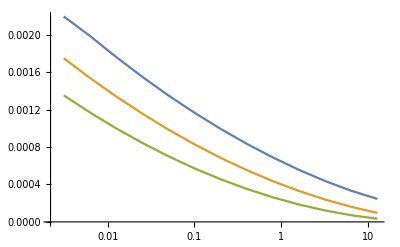

```mathematica
ListLogLinearPlot[{mumu,mua,aa},Joined->True]
```

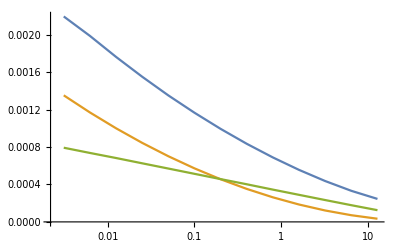

```mathematica
ListLogLinearPlot[{mumu,Dlog,Slog},Joined->True]
```

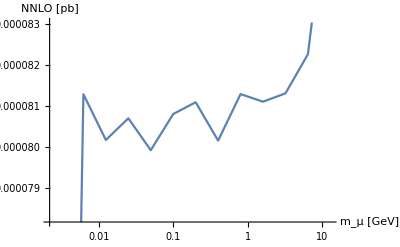

```mathematica
ListLogLinearPlot[diff[diff[mumu,Dlog],Slog],Joined->True,AxesLabel->{"m_μ [GeV]", "NNLO [pb]"}]
```

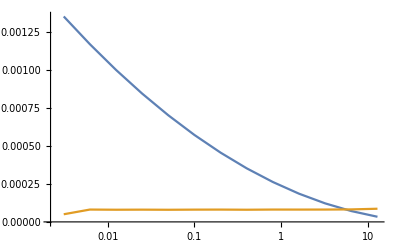

```mathematica
ListLogLinearPlot[{aa,diff[diff[mumu,Dlog],Slog]},Joined->True]
```

```mathematica
diff[diff[mumu,Dlog],Slog]
```

{{0.003125,0.000050327},{0.00625,0.0000812807},{0.0125,0.0000801648},{0.025,0.0000806937},{0.05,0.0000799153},{0.1,0.0000807972},{0.2,0.0000810853},{0.4,0.0000801493},{0.8,0.000081284},{1.6,0.0000810982},{3.2,0.0000813023},{6.4,0.0000822562},{12.8,0.0000867085}}